**************************************************************************************************************************************************
Exercício 2

Cristiano da Silva Benites  /   TIA: 72055065

**************************************************************************************************************************************************

1.	Verifique a documentação da função CellularAutomaton (e o tutorial relativo a Cellular Automata), observando suas parametrizações possíveis. Em particular, entenda a equivalência entre as seguintes formas:

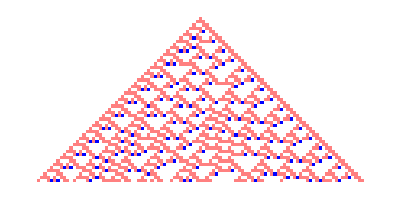
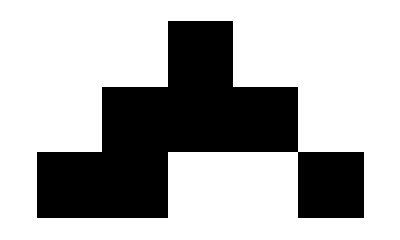
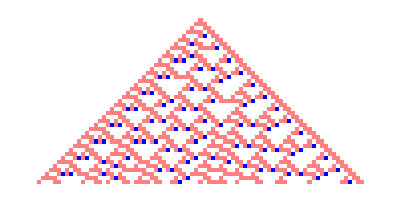
a)  
CellularAutomaton - Documentação:
Sintaxes possíveis:
CellularAutomaton[regra,inicialização,t] 
- gera uma lista que representa a evolução do autômato celular com a regra especificada da condição inicial init para t passos.
CellularAutomaton[regra,init] 
- fornece o resultado da evolução do init para um passo.
CellularAutomaton[regra,inicialização,{tspec,xspec,...}] 
- fornece apenas as partes da evolução especificadas por tspec,xspec,etc.
CellularAutomaton[regra,inicial,{t,All,...}] 
- inclui em cada etapa todas as células que podem ser afetadas ao longo dos t passos.
CellularAutomaton[regra] 
- é uma forma de operador de CellularAutomaton que representa um passo da evolução.

Exemplos básicos de uso:

Execute a regra 30 para 2 passos:
-CellularAutomaton[30,{0,0,0,1,0,0,0},2]
-{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0}}

Execute por 50 passos de um único 1 em um background de 0s:
-ArrayPlot[CellularAutomaton[30,{{1},0},50]]

-Graphics-
Gere um ícone para uma regra de autômato celular sem e com a configuração de CollorRules:
-RulePlot[CellularAutomaton[30]]

-Graphics-

-RulePlot[CellularAutomaton[{679458, 3}],ColorRules->{1->Pink,2->Blue}]

-Graphics-

Escopo:
Regras de uma dimensão

Regra elementar 73:
-CellularAutomaton[73,{{1},0},4]//Grid

0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1

Gere o mesmo resultado usando RulePlot e ArrayPlot:
-RulePlot[CellularAutomaton[73],{{1},0},50]

-Graphics-

-ArrayPlot[CellularAutomaton[73,{{1},0},50]]

-Graphics-

Regra de 2 cores para 679458:
-ArrayPlot[CellularAutomaton[{679458, 3}, {{1}, 0}, 50]]

-Graphics-

Regra de 3 cores para 679458:
-ArrayPlot[CellularAutomaton[{679458, 3}, {{1}, 0}, 50],ColorRules->{1->Pink,2->Blue}]

-Graphics-

Regra totalística de 3 cores (branco, preto e cinza) com código 867:

Definição de regra totalistic: Os ACs totalísticos são autômatos celulares cujo valor de uma célula depende apenas da soma dos valores dos seus vizinhos no passo de tempo anterior (WOLFRAM, 1983). De forma análoga, pode-se considerar que as transições dependem da média dos valores das células que compõem a vizinhança. Já os ACs semi-totalısticos (outer-totalistic CA) são generalizações de ACs cabalísticos (PHILLIPS; WEISSTEIN, 2015). Um AC é considerado semi-totalıstico caso suas transições sejam definidas pela soma (ou média) das células da vizinhança sem levar em consideração a célula central.
Por exemplo, no applet do jogo da vida, para uma célula manter-se viva é necessário que a quantidade de células vivas ao redor seja dois ou três. Esse tipo de representação das regras é chamado de totalístico. Já os ACs semi-totalısticos (outer-totalistic CA) s˜ao generalizações de ACs totalısticos(PHILLIPS; WEISSTEIN, 2015). Um AC é considerado semi-totalistic caso suas transições sejam definidas pela soma (ou média) das células da vizinhança sem levar em consideração a célula central.

Fontes: https://www.cin.ufpe.br/~if114/Monografias/Automatos%20Celulares/especificacoes.htm Acesso em 15/10/2021
SOARES JUNIOR, Zorandir et al. Diferença entre templates de autômatos celulares unidimensionais binários. 2016.

-ArrayPlot[CellularAutomaton[{867, {3, 1}},{{1}, 0}, 50]]

-Graphics-

Intervalo de 2 cores - r == 3/2 (dois vizinhos à esquerda e um à direita, lembrando a convenção de Wolfram da célula deslocada para a direita para raio não inteiro) para regra 23898:
-ArrayPlot[CellularAutomaton[{23898,2,3/2},{{1}, 0}, 40]]

-Graphics-

Uma regra geral range - r == 2:
-ArrayPlot[CellularAutomaton[{39421042,2,2},{{1}, 0}, 40]]

-Graphics-

r == 2 regra totalística com código 10:
-ArrayPlot[CellularAutomaton[{10,{2,1},2},{{1}, 0}, 40]]

-Graphics-

Regra 30 especificada dando deslocamentos explícitos para células em sua vizinhança:
-ArrayPlot[CellularAutomaton[{30,2,{{-1},{0},{1}}},{{1},0},50]]

-Graphics-

Um análogo à regra 30 com deslocamentos modificados de 1 a 2:
-ArrayPlot[CellularAutomaton[{30,2,{{-1},{0},{2}}},{{1},0},50]]

-Graphics-

Uma regra com 2 vizinhos:
-ArrayPlot[CellularAutomaton[{9,2,{{-1},{2}}},{{1},0},50]]

-Graphics-

Regra 30 especificada dando pesos explícitos para células em sua vizinhança:
-ArrayPlot[CellularAutomaton[{30,{2,{4,2,1}}},{{1},0},50]]

-Graphics-

Regra totalística de 3 cores (branco, preto e cinza(azullado)) com código 2049:
-ArrayPlot[CellularAutomaton[{2049, {3, 1}},{{1}, 0}, 50]]

-Graphics-

As regras totalísticas têm peso 1 para cada deslocamento na vizinhança:
-ArrayPlot[CellularAutomaton[{2049, {3, {1,1,1}}},{{1}, 0}, 50]]

-Graphics-


Uma regra semi-totalística de 3 cores:
-ArrayPlot[CellularAutomaton[{50257,{3,{3,1,3}}},{{1},0},50]]

-Graphics-

Especifique a regra 90, dando substituições explícitas para vizinhanças:
-ArrayPlot[CellularAutomaton[{{1,_,1}->0,{1,_,0}->1,{0,_,1}->1,{0,_,0}->0},{{1},0},50]]

-Graphics-

Especifique a regra 90, fornecendo uma única regra de substituição “algébrica”:
-ArrayPlot[CellularAutomaton[{{x_,_,y_}:>Mod[x+y,2]},{{1},0},50]]

-Graphics-

Use uma fórmula booleana explícita para a regra 30, operando nos estados Verdadeiro e Falso:
-CellularAutomaton[{{p_,q_,r_}->Xor[p,Or[q,r]]},{{True},False},2]

{{False,False,True,False,False},{False,True,True,True,False},{True,True,False,False,True}}

-ArrayPlot[Boole[%]]

-Graphics-

Os valores em um autômato celular podem ser qualquer expressão simbólica:
-CellularAutomaton[{{a,_,b}->a,{b,_,a}->b,{x_,_,x_}->a},{{b},a},4]

{{b,a,a,a,a},{a,b,a,a,a},{a,a,b,a,a},{a,a,a,b,a},{a,a,a,a,b}}

Use uma função simbólica arbitrária f como a regra a ser aplicada aos vizinhos de intervalo 1: (*** muito interessante ***)
-CellularAutomaton[{f[#]&,{},1},{a,b,c},1]

{{a,b,c},{f[{c,a,b}],f[{a,b,c}],f[{b,c,a}]}}

Aplique a função aos vizinhos com deslocamentos -1 e 0:
-CellularAutomaton[{f[#]&,{},{{-1},{0}}},{{1},0},2]
-Grid[%]

1 | 0 | 0
f[{0,1}] | f[{1,0}] | f[{0,0}]
f[{f[{0,0}],f[{0,1}]}] | f[{f[{0,1}],f[{1,0}]}] | f[{f[{1,0}],f[{0,0}]}]

Configure um “autômato celular triangular de Pascal”:
-CellularAutomaton[{Total[#]&,{},1/2},{{1},0},3]

{{1,0,0,0},{1,1,0,0},{1,2,1,0},{1,3,3,1}}

Especifique a regra 90 como uma função explícita (Módulo 2):
-ArrayPlot[CellularAutomaton[{Mod[#[[1]]+#[[3]],2]&,{},1},{{1},0},50]]

-Graphics-

Módulo 4 do autômato celular aditivo:
-ArrayPlot[CellularAutomaton[{Mod[Total[#],4]&,{},1},{{1},0},50]]

-Graphics-

O segundo argumento da função é o número do passo:
-CellularAutomaton[{f[#1,#2]&,{},1},{a,b,c},1]

{{a,b,c},{f[{c,a,b},1],f[{a,b,c},1],f[{b,c,a},1]}}

-CellularAutomaton[{f,{},1},{a,b,c},1]

{{a,b,c},{f[{c,a,b},1],f[{a,b,c},1],f[{b,c,a},1]}}

Altere a regra em etapas sucessivas; # 2 fornece o número da etapa:
-ArrayPlot[CellularAutomaton[{Mod[Total[#]+#2,4]&,{},1},{{1},0},30]]

-Graphics-

Use valores contínuos para células:
-ArrayPlot[CellularAutomaton[{Mod[Total[#]/2,1]&,{},1},{{1},0},50]]

-Graphics-

-ArrayPlot[CellularAutomaton[{Mod[Total[#]/2,1]&,{},1},{{1},0},50],ColorFunction->Hue]

-Graphics-

Especifique a regra 90 como uma função booleana pura com Xor ou BooleanFunction :
-ArrayPlot[CellularAutomaton[Xor[#1,#3]&,{{1},0},50]]

-Graphics-

-ArrayPlot[CellularAutomaton[BooleanFunction[90,3],{{1},0},50]]

-Graphics-

Um análogo r == 2 da regra 90 especificado usando uma função booleana pura:
-ArrayPlot[CellularAutomaton[Xor[#1,#5]&,{{1},0},50]]

-Graphics-

Regras especificadas por Associação (*** são as mesmas regras anteriores, mas agora usando uma notação com associação ***)

Especifique a regra 30 usando uma associação:
-ArrayPlot[CellularAutomaton[<|”RuleNumber”→30|>,{{1},0},30]]

-Graphics-

Autômato celular de 3 cores:
-ArrayPlot[CellularAutomaton[<|”RuleNumber”→679458,”Colors”→3|>,{{1}, 0}, 40],ColorRules→{1→Pink,2→Blue}]

-Graphics-

Autômato celular 2 cores gama 3/2:
-ArrayPlot[CellularAutomaton[<|”RuleNumber”→23898,”Range”→3/2|>,{{1}, 0}, 40]]

-Graphics-

Autômato celular totalístico de 3 cores:
-ArrayPlot[CellularAutomaton[<|”TotalisticCode”→867,”Colors”→3|>,{{1}, 0}, 50]]]

-Graphics-

Autômato celular totalístico externo de 3 cores:
-ArrayPlot[CellularAutomaton[<|”OuterTotalisticCode”→50257,”Colors”→3|>,{{1}, 0}, 50]]

-Graphics-

Condições iniciais:

As condições iniciais explícitas são consideradas cíclicas:
-CellularAutomaton[30,{1,0,0,0,0,0},2]

{{1,0,0,0,0,0},{1,1,0,0,0,1},{0,0,1,0,1,1}}

-CellularAutomaton[30,{1,0,0,0,0,0},2]//Grid

1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1

O vizinho esquerdo da célula mais à esquerda é a célula mais à direita e vice-versa:
-CellularAutomaton[{f[#]&,{},1},{a,b,c,d},1]

{{a,b,c,d},{f[{d,a,b}],f[{a,b,c}],f[{b,c,d}],f[{c,d,a}]}}

Condição inicial aleatória:
-ArrayPlot[CellularAutomaton[30,RandomInteger[1,100],50]]

-Graphics-

Comece com uma “semente” (condição inicial) consistindo no bloco 11101 rodeado por 0s:
-ArrayPlot[CellularAutomaton[126,{{1,1,1,0,1},0},20]]

-Graphics-

Comece com um único 0 rodeado por 1s:
-ArrayPlot[CellularAutomaton[150,{{0},1},20]]

-Graphics-

Comece do 111 em um fundo de 10 blocos repetidos:
-ArrayPlot[CellularAutomaton[22,{{1,1,1},{1,0}},20]]

-Graphics-

Especifique a “semente” (condição inicial)  como uma matriz esparsa:
-ArrayPlot[CellularAutomaton[150,{SparseArray[{1->1,10->1}],0},20]]

-Graphics-

Use uma matriz esparsa para fornecer a condição inicial cíclica completa:
-ArrayPlot[CellularAutomaton[150,SparseArray[{1->1,10->1},50],20]]

-Graphics-

Comece a partir do bloco 101 no deslocamento -8 e bloco 11 no deslocamento 9:
-ArrayPlot[CellularAutomaton[150,{{{{1,0,1},{-8}},{{1,1},{9}}},0},20]]

-Graphics-



b) Em particular, entenda a equivalência entre as seguintes formas:

• Boolean functions
(e.g., rule 90 as a pure Boolean function: Xor[#1,#3]& , or simply as BooleanFunction[90,3])

Resposta:
Generate the rule 90 elementary cellular automaton rule:
-f=Function[{v,i},BooleanFunction[90,3]@@v]

Simulate it:

Resposta:
-CellularAutomaton[{f,{},1},{False,False,True,False,False},2]
{{False,False,True,False,False},{False,True,False,True,False},{True,False,False,False,True}}

Compare to the standard encoding:

Resposta:
-Boole[%]
{{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}}

-CellularAutomaton[90,{0,0,1,0,0},2]
{{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}}

• Explicit replacements for neighbourhoods (e.g., rule 90: {{1,_,1}->0, {1,_,0}->1, {0,_,1}->1, {0,_,0}->0}

Resposta:
-CellularAutomaton[{{1,_,1}->0, {1,_,0}->1, {0,_,1}->1, {0,_,0}->0},{0,0,1,0,0},2]
{{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}}


• Single “algebraic” replacement rule (e.g., rule 90: {{x_,_,y_} :> Mod[x+y,2]})

Resposta:
-CellularAutomaton[{{x_,_,y_}:>Mod[x+y,2]},{0,0,1,0,0},2]
{{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}}


•Explicit functions  (e.g., rule 90 as the algebraic function{Mod[#[[1]]+#[[3]],2]&,{},1})

Resposta:
-CellularAutomaton[{Mod[#[[1]]+#[[3]],2]&,{},1},{0,0,1,0,0},2]
{{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}}

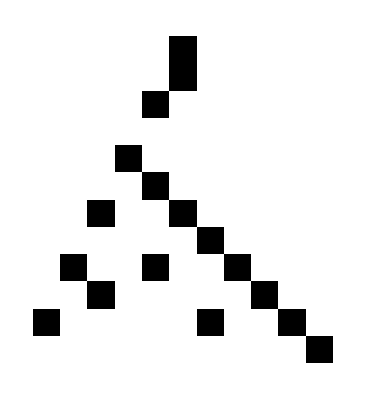
#### 2. Entender o conceito de Second-order rules, definidas como: o próximo estado si no tempo t+1 é função não só de (si-1, si, si+1) no tempo t, mas também de (si-1, si, si+1) no tempo t-1. Em seguida responda: quantas funções locais (regras) existem? a) Entender o conceito de Second-order rules, definidas como: OBS: A definição está na documentação da função CellularAutomaton. - o próximo estado si no tempo t+1 é função não só de (si-1, si, si+1) no tempo t, mas também de (si-1, si, si+1) no tempo t-1. (In an order-s cellular automaton, specified by {rule,kspec,rspec,s}, each step depends on s preceding steps) Resposta: Higher-Order Rulers Rule 30 written out explicitly as a “first-order rule”: -CellularAutomaton[{30,2,1,1},{{1,0,1,1}},4] {{1,0,1,1},{0,0,1,0},{0,1,1,1},{0,1,0,0},{1,1,1,0}} A second-order analog of rule 30, involving two steps of initial conditions: -CellularAutomaton[{30,2,1,2},{{1,0,1,1},{1,1,0,1}},4] {{1,1,0,1},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} Include both initial-condition steps in the output: -CellularAutomaton[{30,2,1,2},{{1,0,1,1},{1,1,0,1}},{{-1,4}}] {{1,0,1,1},{1,1,0,1},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} Second-order rule 1008, starting with a single 1 in both initial condition steps: -ArrayPlot[CellularAutomaton[{1008,2,1,2},{{{1},{1}},0},40]] -Graphics- Include both steps in the initial conditions: -ArrayPlot[CellularAutomaton[{1008,2,1,2},{{{1},{1}},0},{{-1,10}}]] -Graphics- Second-order totalistic rule 10 with 2 colors and range 1: -ArrayPlot[CellularAutomaton[{10,{2,1},1,2},{{{1},{1}},0},50]] -Graphics- A 12^th-order version of the same rule (10): -ArrayPlot[CellularAutomaton[{10,{2,1},1,12},{Table[{1},{12}],0},50]] -Graphics- Rule 150R—the second-order reversible mod 2 rule (usa o Flatten para todos ficarem no mesmo nivel para poder rodar o módulo): -ArrayPlot[CellularAutomaton[{Mod[Total[Flatten[#]],2]&,{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},127]] -Graphics- A spacetime slice of a second-order totalistic rule (97852) with 2 colors and range 1: -ArrayPlot[First/@CellularAutomaton[{97852,{2,1},{1,1},2},{{{{1}},{{1}}},0},{50,{0},All}]] -Graphics- Step 50 of the same rule(97852): -ArrayPlot[First@CellularAutomaton[{97852,{2,1},{1,1},2},{{{{1}},{{1}}},0},{{50},All,All}]] -Graphics- b) Em seguida responda: quantas funções existem? Resposta (conforme orientação do Professor PP): Considerando as 6 células como se elas constituíssem um AC unidimensional de raio 2.5. * * * passo t-1 * * * passo t * * * * * * passo t (de segunda ordem) (convenção do CA referencia a mais deslocada para a direita) Se o sentido da palavra “função” for regra, então: A vizinhança do AC em questão possui (r=2,5, k=2). Portanto k^(k^(2r+1))temos: 2^(2^(2,5) +1) = 2^(2^6) = 2^(64) = 18.446.744.073.709.551.616 funções 3. Entender o conceito de regras confinadas (Captive) e analisar sua ocorrência no espaço elementar (i.e., quantas e quais são as regras?). OBS: A definição se encontra no CAMat.nb. a) Entender o conceito de regras confinadas (Captive) OBS: A definição se encontra no CAMat.nb. “Os autômatos celulares confinados (do inglês, captive), são uma classe de ACs que se baseiam em uma caracterização de suas funções locais que não adotem estados definidos em qualquer estrutura externa à vizinhança (THEYSSIER, 2004). Theyssier (2004) formalmente define que, dada a função local f de um AC para a vizinhança (α0,...,α2r), sendo o r o raio, um AC é considerado confinado se respeitar a condição descrita na Eq. (10). f ((α(0) , ..., α(2r) )) = β, sendo β ∈ {α(0) , ..., α(2r) } (10) Naturalmente, qualquer AC binário que tenha as funções locais f((0(0),0(1),...,0(2r))) = 0 e f((1(0),1,1...,1(2r))) = 1 é um AC confinado.” Fonte: SOARES JUNIOR, Zorandir et al. Diferença entre templates de autômatos celulares uni-dimensionais binários. 2016. b) analisar sua ocorrência no espaço elementar (i.e., quantas e quais são as regras?) Resposta: Fazer um loop de 0 até 255 com contador de “trues” e imprimir o número da regra durante o loop: rnum varia de 1 a 256 para todas as regras do espaço elementar, k=2 (2 estados), r=1 (vizinhança=3) rnum=1 cont = 0 a={}; Do[If[CaptiveQ[rnum,2,1],a=Append[a,rnum];cont++];rnum++,256]; rnum a 4. a) Entender o conceito de regras com um estado de espalhamento (Spreading). OBS: A definição se encontra no CAMat.nb. Achei um artigo muito interessante sobre espalhamento, é muito parecido com o que estamos vendo em Sistemas Dinâmicos: BAGNOLIA, F.; RECHTMANB, R.; RUFFOB, S. Damage spreading and Lyapunov exponents in cellular automata. arXiv preprint cond-mat/9811159, 2008. Resposta: Estado de propagação: para o conjunto de estados S e vizinhança com células n, ou seja, s(1), ..., s(n)), s(j) E S), s(s) é um estado de espalhamento <=> f(s(1), ..., s(n)) = s(s), quando s(s) E {s(1), ..., s(n0} e f(s(1), ..., s(n)) !E s(s), quando s(s) !E {s(1), ..., s(n)}. OBS: Só pode existir um único estado de espalhamento para qualquer CA. Spreading state CA: é aquele que possui um estado spread. b) Analisar sua ocorrência nos espaços elementar e de raio 1.5. Resposta: **** NÃO FUCIONOU, NÃO ENTENDI PORQUE **** Fazer um loop de 0 até 255 com contador de “trues” e imprimir o número da regra durante o loop: rnum varia de 1 a 256 para todas as regras do espaço elementar, k=2 (2 estados), r=1.5 (vizinhança=4) rnum=1 cont = 0 a={}; Do[If[SpreadingStateQ[rnum,2,1.5],a=Append[a,rnum];cont++];rnum++,256]; rnum a 1. Função CellularAutomaton a) Verifique a documentação da função CellularAutomaton (e o tutorial relativo a Cellular Automata), observando suas parametrizações possíveis. Resposta da questão 1: CellularAutomaton - Documentação: Sintaxes possíveis: CellularAutomaton[regra,inicialização,t] - gera uma lista que representa a evolução do autômato celular com a regra especificada da condição inicial init para t passos. CellularAutomaton[regra,init] - fornece o resultado da evolução do init para um passo. CellularAutomaton[regra,inicialização,{tspec,xspec,...}] - fornece apenas as partes da evolução especificadas por tspec,xspec,etc. CellularAutomaton[regra,inicial,{t,All,...}] - inclui em cada etapa todas as células que podem ser afetadas ao longo dos t passos. CellularAutomaton[regra] - é uma forma de operador de CellularAutomaton que representa um passo da evolução. Exemplos básicos de uso: Execute a regra 30 para 2 passos: -CellularAutomaton[30,{0,0,0,1,0,0,0},2] -{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0}} Execute por 50 passos de um único 1 em um background de 0s: -ArrayPlot[CellularAutomaton[30,{{1},0},50]] -Graphics- Gere um ícone para uma regra de autômato celular sem e com a configuração de CollorRules: -RulePlot[CellularAutomaton[30]] -Graphics- -RulePlot[CellularAutomaton[{679458, 3}],ColorRules->{1->Pink,2->Blue}] -Graphics- Escopo: Regras de uma dimensão Regra elementar 73: -CellularAutomaton[73,{{1},0},4]//Grid 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 Gere o mesmo resultado usando RulePlot e ArrayPlot: -RulePlot[CellularAutomaton[73],{{1},0},50] -Graphics- -ArrayPlot[CellularAutomaton[73,{{1},0},50]] -Graphics- Regra de 2 cores para 679458: -ArrayPlot[CellularAutomaton[{679458, 3}, {{1}, 0}, 50]] -Graphics- Regra de 3 cores para 679458: -ArrayPlot[CellularAutomaton[{679458, 3}, {{1}, 0}, 50],ColorRules->{1->Pink,2->Blue}] -Graphics- Regra totalística de 3 cores (branco, preto e cinza) com código 867: Definição de regra totalística: Os ACs totalísticos são autômatos celulares cujo valor de uma célula depende apenas da soma dos valores dos seus vizinhos no passo de tempo anterior (WOLFRAM, 1983). De forma análoga, pode-se considerar que as transições dependem da média dos valores das células que compõem a vizinhança. Já os ACs semi-totalısticos (outer-totalistic CA) são generalizações de ACs totalísticos (PHILLIPS; WEISSTEIN, 2015). Um AC é considerado semi-totalıstico caso suas transições sejam definidas pela soma (ou média) das células da vizinhança sem levar em consideração a célula central. Por exemplo, no applet do jogo da vida, para uma célula manter-se viva é necessário que a quantidade de células vivas ao redor seja dois ou três. Esse tipo de representação das regras é chamado de totalístico. Já os ACs semi-totalısticos (outer-totalistic CA) s˜ao generalizaç˜oes de ACs totalısticos(PHILLIPS; WEISSTEIN, 2015). Um AC é considerado semi-totalıstico caso suas transiç˜oessejam definidas pela soma (ou média) das células da vizinhança sem levar em consideraç˜aoa célula central. Fontes: https://www.cin.ufpe.br/~if114/Monografias/Automatos%20Celulares/especificacoes.htm Acesso em 06/10/2020 SOARES JUNIOR, Zorandir et al. Diferença entre templates de autômatos celulares unidimensionais binários. 2016. -ArrayPlot[CellularAutomaton[{867, {3, 1}},{{1}, 0}, 50]] -Graphics- Intervalo de 2 cores - r == 3/2 (dois vizinhos à esquerda e um à direita, lembrando a convenção de Wolfram da célula deslocada para a direita para raio não inteiro) para regra 23898: -ArrayPlot[CellularAutomaton[{23898,2,3/2},{{1}, 0}, 40]] -Graphics- Uma regra geral range - r == 2: -ArrayPlot[CellularAutomaton[{39421042,2,2},{{1}, 0}, 40]] -Graphics- r == 2 regra totalística com código 10: -ArrayPlot[CellularAutomaton[{10,{2,1},2},{{1}, 0}, 40]] -Graphics- Regra 30 especificada dando deslocamentos explícitos para células em sua vizinhança: -ArrayPlot[CellularAutomaton[{30,2,{{-1},{0},{1}}},{{1},0},50]] -Graphics- Um análogo à regra 30 com deslocamentos modificados de 1 a 2: -ArrayPlot[CellularAutomaton[{30,2,{{-1},{0},{2}}},{{1},0},50]] -Graphics- Uma regra com 2 vizinhos: -ArrayPlot[CellularAutomaton[{9,2,{{-1},{2}}},{{1},0},50]] -Graphics- Regra 30 especificada dando pesos explícitos para células em sua vizinhança: -ArrayPlot[CellularAutomaton[{30,{2,{4,2,1}}},{{1},0},50]] -Graphics- Regra totalística de 3 cores (branco, preto e cinza(azullado)) com código 2049: -ArrayPlot[CellularAutomaton[{2049, {3, 1}},{{1}, 0}, 50]] -Graphics- As regras totalísticas têm peso 1 para cada deslocamento na vizinhança: -ArrayPlot[CellularAutomaton[{2049, {3, {1,1,1}}},{{1}, 0}, 50]] -Graphics- Uma regra semi-totalística de 3 cores: -ArrayPlot[CellularAutomaton[{50257,{3,{3,1,3}}},{{1},0},50]] -Graphics- Especifique a regra 90, dando substituições explícitas para vizinhanças: -ArrayPlot[CellularAutomaton[{{1,_,1}->0,{1,_,0}->1,{0,_,1}->1,{0,_,0}->0},{{1},0},50]] -Graphics- Especifique a regra 90, fornecendo uma única regra de substituição “algébrica”: -ArrayPlot[CellularAutomaton[{{x_,_,y_}:>Mod[x+y,2]},{{1},0},50]] -Graphics- Use uma fórmula booleana explícita para a regra 30, operando nos estados Verdadeiro e Falso: -CellularAutomaton[{{p_,q_,r_}->Xor[p,Or[q,r]]},{{True},False},2] {{False,False,True,False,False},{False,True,True,True,False},{True,True,False,False,True}} -ArrayPlot[Boole[%]] -Graphics- Os valores em um autômato celular podem ser qualquer expressão simbólica: -CellularAutomaton[{{a,_,b}->a,{b,_,a}->b,{x_,_,x_}->a},{{b},a},4] {{b,a,a,a,a},{a,b,a,a,a},{a,a,b,a,a},{a,a,a,b,a},{a,a,a,a,b}} Use uma função simbólica arbitrária f como a regra a ser aplicada aos vizinhos de intervalo 1: (*** muito interessante ***) -CellularAutomaton[{f[#]&,{},1},{a,b,c},1] {{a,b,c},{f[{c,a,b}],f[{a,b,c}],f[{b,c,a}]}} Aplique a função aos vizinhos com deslocamentos -1 e 0: -CellularAutomaton[{f[#]&,{},{{-1},{0}}},{{1},0},2] -Grid[%] 1 | 0 | 0 f[{0,1}] | f[{1,0}] | f[{0,0}] f[{f[{0,0}],f[{0,1}]}] | f[{f[{0,1}],f[{1,0}]}] | f[{f[{1,0}],f[{0,0}]}] Configure um “autômato celular triangular de Pascal”: -CellularAutomaton[{Total[#]&,{},1/2},{{1},0},3] {{1,0,0,0},{1,1,0,0},{1,2,1,0},{1,3,3,1}} Especifique a regra 90 como uma função explícita (Módulo 2): -ArrayPlot[CellularAutomaton[{Mod[#[[1]]+#[[3]],2]&,{},1},{{1},0},50]] -Graphics- Módulo 4 do autômato celular aditivo: -ArrayPlot[CellularAutomaton[{Mod[Total[#],4]&,{},1},{{1},0},50]] -Graphics- O segundo argumento da função é o número do passo: -CellularAutomaton[{f[#1,#2]&,{},1},{a,b,c},1] {{a,b,c},{f[{c,a,b},1],f[{a,b,c},1],f[{b,c,a},1]}} -CellularAutomaton[{f,{},1},{a,b,c},1] {{a,b,c},{f[{c,a,b},1],f[{a,b,c},1],f[{b,c,a},1]}} Altere a regra em etapas sucessivas; # 2 fornece o número da etapa: -ArrayPlot[CellularAutomaton[{Mod[Total[#]+#2,4]&,{},1},{{1},0},30]] -Graphics- Use valores contínuos para células: -ArrayPlot[CellularAutomaton[{Mod[Total[#]/2,1]&,{},1},{{1},0},50]] -Graphics- -ArrayPlot[CellularAutomaton[{Mod[Total[#]/2,1]&,{},1},{{1},0},50],ColorFunction->Hue] -Graphics- Especifique a regra 90 como uma função booleana pura com Xor ou BooleanFunction : -ArrayPlot[CellularAutomaton[Xor[#1,#3]&,{{1},0},50]] -Graphics- -ArrayPlot[CellularAutomaton[BooleanFunction[90,3],{{1},0},50]] -Graphics- Um análogo r == 2 da regra 90 especificado usando uma função booleana pura: -ArrayPlot[CellularAutomaton[Xor[#1,#5]&,{{1},0},50]] -Graphics- Regras especificadas por Associação (*** são as mesmas regras anteriores, mas agora usando uma notação com associação ***) Especifique a regra 30 usando uma associação: -ArrayPlot[CellularAutomaton[<|”RuleNumber”→30|>,{{1},0},30]] -Graphics- Autômato celular de 3 cores: -ArrayPlot[CellularAutomaton[<|”RuleNumber”→679458,”Colors”→3|>,{{1}, 0}, 40],ColorRules→{1→Pink,2→Blue}] -Graphics- Autômato celular 2 cores gama 3/2: -ArrayPlot[CellularAutomaton[<|”RuleNumber”→23898,”Range”→3/2|>,{{1}, 0}, 40]] -Graphics- Autômato celular totalístico de 3 cores: -ArrayPlot[CellularAutomaton[<|”TotalisticCode”→867,”Colors”→3|>,{{1}, 0}, 50]]] -Graphics- Autômato celular totalístico externo de 3 cores: -ArrayPlot[CellularAutomaton[<|”OuterTotalisticCode”→50257,”Colors”→3|>,{{1}, 0}, 50]] -Graphics- Condições iniciais: As condições iniciais explícitas são consideradas cíclicas: -CellularAutomaton[30,{1,0,0,0,0,0},2] {{1,0,0,0,0,0},{1,1,0,0,0,1},{0,0,1,0,1,1}} -CellularAutomaton[30,{1,0,0,0,0,0},2]//Grid 1 | 0 | 0 | 0 | 0 | 0 1 | 1 | 0 | 0 | 0 | 1 0 | 0 | 1 | 0 | 1 | 1 O vizinho esquerdo da célula mais à esquerda é a célula mais à direita e vice-versa: -CellularAutomaton[{f[#]&,{},1},{a,b,c,d},1] {{a,b,c,d},{f[{d,a,b}],f[{a,b,c}],f[{b,c,d}],f[{c,d,a}]}} Condição inicial aleatória: -ArrayPlot[CellularAutomaton[30,RandomInteger[1,100],50]] -Graphics- Comece com uma “semente” (condição inicial) consistindo no bloco 11101 rodeado por 0s: -ArrayPlot[CellularAutomaton[126,{{1,1,1,0,1},0},20]] -Graphics- Comece com um único 0 rodeado por 1s: -ArrayPlot[CellularAutomaton[150,{{0},1},20]] -Graphics- Comece do 111 em um fundo de 10 blocos repetidos: -ArrayPlot[CellularAutomaton[22,{{1,1,1},{1,0}},20]] -Graphics- Especifique a “semente” (condição inicial) como uma matriz esparsa: -ArrayPlot[CellularAutomaton[150,{SparseArray[{1->1,10->1}],0},20]] -Graphics- Use uma matriz esparsa para fornecer a condição inicial cíclica completa: -ArrayPlot[CellularAutomaton[150,SparseArray[{1->1,10->1},50],20]] -Graphics- Comece a partir do bloco 101 no deslocamento -8 e bloco 11 no deslocamento 9: -ArrayPlot[CellularAutomaton[150,{{{{1,0,1},{-8}},{{1,1},{9}}},0},20]] -Graphics- b) Em particular, entenda a equivalência entre as seguintes formas: • Boolean functions (e.g., rule 90 as a pure Boolean function: Xor[#1,#3]& , or simply as BooleanFunction[90,3]) Resposta: Generate the rule 90 elementary cellular automaton rule: -f=Function[{v,i},BooleanFunction[90,3]@@v] Simulate it: Resposta: -CellularAutomaton[{f,{},1},{False,False,True,False,False},2] {{False,False,True,False,False},{False,True,False,True,False},{True,False,False,False,True}} Compare to the standard encoding: Resposta: -Boole[%] {{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}} -CellularAutomaton[90,{0,0,1,0,0},2] {{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}} • Explicit replacements for neighbourhoods (e.g., rule 90: {{1,_,1}->0, {1,_,0}->1, {0,_,1}->1, {0,_,0}->0} Resposta: -CellularAutomaton[{{1,_,1}->0, {1,_,0}->1, {0,_,1}->1, {0,_,0}->0},{0,0,1,0,0},2] {{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}} • Single “algebraic” replacement rule (e.g., rule 90: {{x_,_,y_} :> Mod[x+y,2]}) Resposta: -CellularAutomaton[{{x_,_,y_}:>Mod[x+y,2]},{0,0,1,0,0},2] {{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}} •Explicit functions (e.g., rule 90 as the algebraic function{Mod[#[[1]]+#[[3]],2]&,{},1}) Resposta: -CellularAutomaton[{Mod[#[[1]]+#[[3]],2]&,{},1},{0,0,1,0,0},2] {{0,0,1,0,0},{0,1,0,1,0},{1,0,0,0,1}}